```mathematica
ParametricPolarPlot[{r_, θ_}, range_, opts:OptionsPattern[]]:=
ParametricPlot[{r*Cos[θ], r*Sin[θ]}, range, opts]
```

```mathematica
ListPolarLinePlot[polarPointList:{{_,_}...}, opts:OptionsPattern[]]:=
ListLinePlot[polarPointList/.{r_, θ_}:>{r*Cos[θ], r*Sin[θ]}, opts]
```

```mathematica
TManip[t_] := t+Sin[t*5]*0.05+Sin[t+Pi/2]*0.2;
```

```mathematica
InverseTManip := InverseFunction[TManip]
```

```mathematica
SplatFunction[t_, n_, r_] :={r-(r+.5)*Cos[n t]/n, InverseTManip[t+1.5*Sin[n t]/n]}
```

```mathematica
Manipulate[
ParametricPolarPlot[
SplatFunction[TManip[t], n, r], {t, 0, 2Pi}],
{n, 8, 15, 1},
{r,1,4}]
```

```mathematica
RandomPaintSplatter[colorScheme_] :=
Module[{lobes,radius, phase, color},
lobes := Evaluate[RandomInteger[{8,15}]];
radius := Evaluate[RandomReal[{0.5,1.5}]];
phase := Evaluate[RandomReal[{0,Pi/2}]];
color := Evaluate[colorScheme[Random[]]];
ListPolarLinePlot[
Table[
SplatFunction[t, lobes, radius],
{t,0, 2 Pi, Pi/100}],
PlotStyle->None,
Filling->0,
AspectRatio->1,
FillingStyle->color]]
```

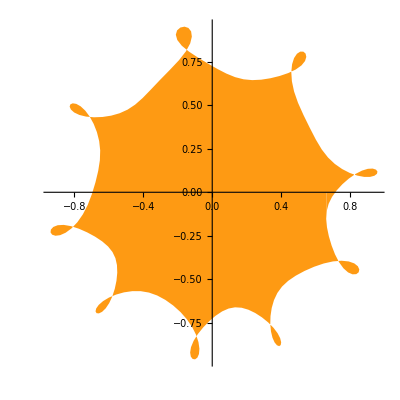

```mathematica
RandomPaintSplatter[ColorData["SolarColors"]]
```

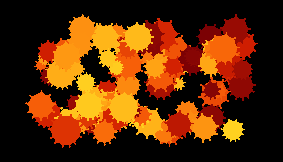

```mathematica
Show[
Table[
Graphics[
Translate[
RandomPaintSplatter[ColorData["SolarColors"]][[1]], {Random[Real,{-10,10}], Random[Real,{-5,5}]}]],
{i,0,100}],
Background -> Black,
ImageSize -> 10*72/2.54]
```